# Artificial Neural Netwok

## Courses for Emma

Baoxiang Pan
2016.9. 13

## Basic Structure

```mathematica
-Graphics--Graphics-
```

### What characterizes an ANN?

How many layers?

How many neurons in each layer?

How does each neuron function on its inputs?

### Neuron Functions (Activation Functions)

Identity

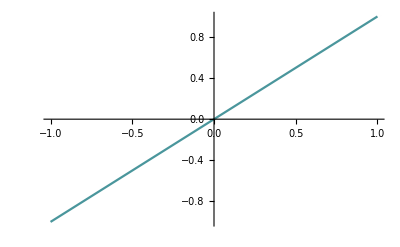

```mathematica
fid[x_]:=x
Plot[fid[x],{x,-1,1}]
```

Binary Step

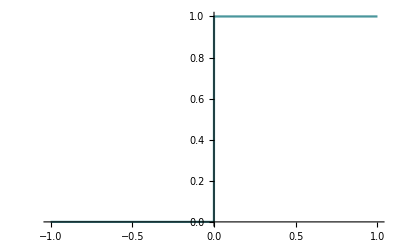

```mathematica
fbs[x_]:=If[x<0,0,1]
Plot[fbs[x],{x,-1,1}]
```

Logistic

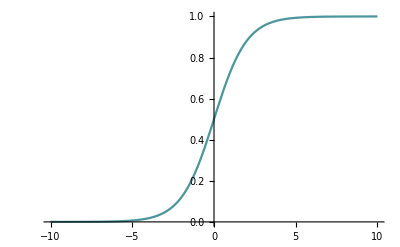

```mathematica
flg[x_]:=1/(1+Exp[-x])
Plot[flg[x],{x,-10,10}]
```

Tanh

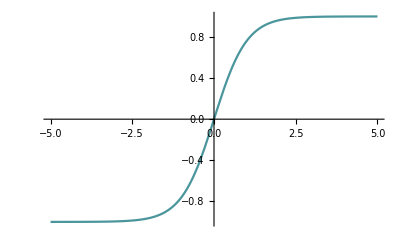

```mathematica
ftanh[x_]:=Tanh[x]
Plot[ftanh[x],{x,-5,5}]
```

ArcTan

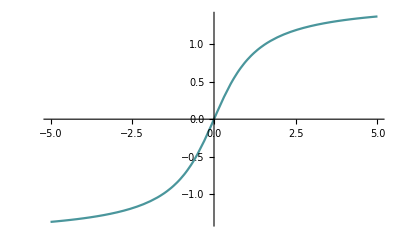

```mathematica
farct[x_]:=ArcTan[x]
Plot[farct[x],{x,-5,5}]
```

Gaussian

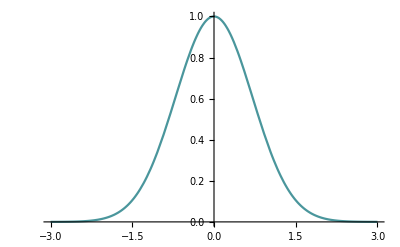

```mathematica
fgs[x_]:=Exp[-x^2]
Plot[fgs[x],{x,-3,3}]
```

## How neurons combine?

The anwser is to give each neuron a weight and add them together!

### Classification/Regression/P.D.F Estimation Example of ANN

```mathematica
Hyperlink["UCI Machine Learning Dataset","http://archive.ics.uci.edu/ml/datasets.html"]
```

#### Problem Description:

Beauty or Ugly? A stupid coorporation believes that there are 3 dorminant features that can determine if a women is beutiful or ugly. These features are:

If her left and right eye distance is less than 6 cm

If her breast is wider than her butt

If she has long hair

They now have 4 girls as their data source. Two of them are recognized as beauty by the public while unfortunately the rest two are thought as ugly. 
Now we represent the dataset in the following manner:

Each row represent a girl’s information. For example, the first row means the girl whose eye distance is not less than 6 cm(0 indicates no to the firs feature), whose breast is not larger than her butt(0), who has long hair(1), is not a beauty(0). 
Now we want to build an ANN which could tell us if a girl is a beauty or not given her three features.

#### Problem Analysis:

### Remember what characterizes an ANN?

How many layers?

This is an easy problem. Let’s suppose 3 layers (one input, one middle layer and one output layer can solve it). If it’s not working well, we can increase the layers to cope with the more difficult conditions.

How many neurons in each layer?

For the input layer, we have three features to be considered, so the neuron number for the input layer is 3. 
Again, since it is an easy question, let’s suppose, maybe 3 neurons in the second layer can solve it. If it can’t, we can just add more neurons to deal with harder conditions.
For the output layer, we want the ANN to tell us if she is a beauty(1) or not(0). A single neuron can do that, if the value of the neuron is larger than a pre-fixed value, for example, 0.5, then we think she is a beauty, otherwise, she is not.

How does each neuron function on its inputs?

Let’s just use identical function. If it’s not working, we can try others (logistic, tanh, Gaussian, etc.).

#### Problem Solvent:

Assume some priori weights for each neuron connection:

For the first girl,

x1=0

x2=0

x3=1

And her score is 0, which means she is ugly.

Here, for each of the neuron in the second layer, its input is from its former layer, which is the input layer. So, each neuron should be allocated with 3 weights. Together there are 3x3 weights to connect the firs and second layers. 
for the only neuron in th third layer, it should be connected with  each neuron in the second layer, so there are 3 weights that we should allocate.

After we get the weighted sumed input for the 3rd layer neuron, we can have a logistic or some other funtions that transform the input to output. Again, the selection of the function form is totally arbitrary. We are just trying to apply small simple functions to simulate more complex activities by trial and error, which is the power of ANN.

Let’s do it!

First, we just generate some random numbers as the intial weights.
A 3x3 weight matrix is generated to connect the first layer (input layer) and the second layer.

```mathematica
weight12=MatrixForm[Table[RandomReal[{-1,1}],{i,1,3},{j,1,3}]]
```

(-0.285996 | 0.166471 | 0.760927
0.348088 | 0.0197081 | -0.442068
-0.119332 | -0.257621 | 0.698159)

wij means the weight connecting the jth neuron in the 1st layer to the ith neuron  in the second layer.

Let’s review some linear algebra.

For the first girl, as we have mensioned (x1,x2,x3)=(0,0,1), given the weight12 matrix:

(-0.285996 | 0.166471 | 0.760927
0.348088 | 0.0197081 | -0.442068
-0.119332 | -0.257621 | 0.698159)

a1=x1*w11+x2*w12+x3*w13
a2=x1*w21+x2*w22+x3*w23
a1=x1*w31+x2*w32+x3*w33
Write it  in the matrix form, we have:
(w11 | w12 | w13
w21 | w22 | w23
w31 | w32 | w33)*(x1
x2
x3)=(a1
a2
a3)

For the second and third layer, please write out the matrix from.

(ww11 | ww12 | ww13)*(a1
a2
a3)=Result

As long as we have the weights, we have built our firs neuron network!

Predict=F[(ww11 | ww12 | ww13)*(w11 | w12 | w13
w21 | w22 | w23
w31 | w32 | w33)*(x1
x2
x3)]

The next step is to see how the predict is different from the observation, and adjust the predict by tuning the parameters in the equation above, specifically, we should adjust wij and ww ij. The most common method is Back Propagation.

## But how can I determine the weights?

Before digging into the technical details, let’s first clarify the objective for classification/regression/p.d.f. estimation?

## Objective for Parameter Estimation

The problem of classification/regression is typically solved by minimizing the "difference" between the study objective's features and their corresponding simulations. The specific strategies may include tuning the constitutive function forms or function parameters using either analytical or trial and error methods.  
    For Artificial Neural Network, once we have decided the layer number, neuron number for each layer and the activation function of each neuron, we have setted down the constitutive function form. The rest work is to tune the parameters. Given the good structure of the network, we can apply the analytical method to gradually tune the parameters (weights between connections). 
    The mathematical expression of the difference between reality and model is termed as objective function. Objecive functions should match and quantify our intuition about how close the model fits the research object, which is partially known given the imperfect and incomplete observations.
     The most intuitive objective function  is the norm of the observation simulation residual vector. Norm is a function that assigns a strictly positive length or size to each vector in a vector space—save for the zero vector, which is assigned a length of zero. For example, the 2-norm, named Euclidean distance, is widely used for estimator fitting.
     While this function balances the mismatch of each observation simulation pair with equal weight and results in average estimation for linear models, it is criticized for the ignorance of observation variance and heteroscedasticity as revealed by data.  We will deal with these issues after grasping BP ANN. Just to remind you that a guy won Nobel Economy Medal for his contribution in this area.

## Strategy for Parameter Estimation

As is mentioned in the previous page, two strategies are applied for parameter estimation:
analytical and trial and error. Analytical means applying gradience of penalty or objective functions to seek its optimal, which is usually effective and fast. Trial and error is applied when the penalty or objective funtion has no specifical forms and can not get its gradience.

Now let’s look at the ANN model form of the previous example,

Predict=F[(ww11 | ww12 | ww13)*(w11 | w12 | w13
w21 | w22 | w23
w31 | w32 | w33)*(x1
x2
x3)]

For each girl, we have her x1,x2,x3 and the judgement (model result) that if she is beautiful or not. Since we have 4 girls, we have correspondent 4 predicts and 4 observations, we can write the Euclidean distance of the model error :
    F=(Predict_1-Observe_1)^2+(Predict_2-Observe_2)^2+(Predict_3-Observe_3)^2+(Predict_4-Observe_4)^2

Now we can write down the spefic formula of the objective function, and make derivative of it. That means, it is analyticable.
    I will show you why if we go along the gradience direction we can reach the maximum or minimum of the function.

## Why Gradience

## Gradience of Neural Network

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

## Slide

This is a text cell.

-Graphics-

-Graphics-

## Examples Applying Back Propogation Training

## Drawbacks of Back Propagation

Deep Neural Network